## Function Documentation

### This is a clickable list of functions and keywords that provide some documentation

```mathematica
?Mechanisms`*
```

```mathematica
?Mechanisms`geometry`*
```

```mathematica
?Mechanisms`rigidity`*
```

```mathematica
?Mechanisms`Origami`*
```

```mathematica
?Mechanisms`graphics`*
```

## Functions

### cells

A cell has the form
	head[ indices ]
where head is one these

```mathematica
DefaultCellData[]
```

{RigidBar,Spring,Face,ElasticTriangle,TorsionalFold,FreeJoint,PinnedJoint,AngleJoint}

You can also have a head that is an arbitrary string. These are called tags and can be used to store information about cells of a mechanism.

Cells have properties which can be found by calling DefaultCellData[] (these properties are strings)

```mathematica
DefaultCellData[RigidBar]
```

{EquilibriumLength→Automatic,Stiffness→∞}

There are additional properties for all cells “Shape”, “Style”, and “Label”.

### specifying cells and their properties

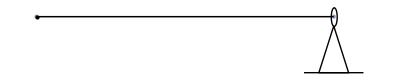

```mathematica
m=Linkage[{{0,0},{1,0}},{RigidBar[{1,2}],PinnedJoint[2]}]
```

You can include several sets of indices in each cell.

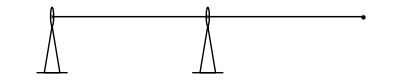

```mathematica
m=Linkage[{{0,0},{1,0},{2,0}},{RigidBar[{{1,2},{2,3}}],PinnedJoint[{1,2}]}]
```

Cell properties can also be specified. Each cell has three universal properties, “style”, “shape” and “label” which can be used to affect how they are displayed. Other properties can be accessed through defaultData[]

```mathematica
DefaultCellData[RigidBar]
```

{EquilibriumLength→Automatic,Stiffness→∞}

You can specify these in one of two ways

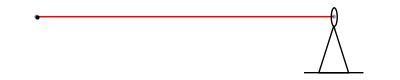

```mathematica
m=Linkage[{{0,0},{1,0}},{Property[RigidBar[{1,2}],"Style"->{Red}],PinnedJoint[2]}]
```

```mathematica
m=Linkage[{{0,0},{1,0}},{RigidBar[{1,2},{"Style"->Red}],PinnedJoint[2]}]
```

-Graphics-

Properties can be nested and can be distributed across several cells.

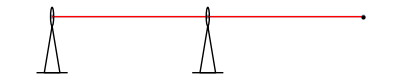

```mathematica
m=Linkage[{{0,0},{1,0},{2,0}},{RigidBar[{{1,2},{2,3}},"Style"->Red],PinnedJoint[{1,2}]}]
```

Unrecognized properties are ignored.

### mechanism types

There are two types of mechanisms with heads framework and origami. These are identical except for how they render.

All mechanisms are defined similarly to how MeshRegion[] objects are defined in Mathematica.

Linkage[ list of coordinates, list of cells]
Origami[ list of coordinates, list of cells]

They take the same options as MeshRegion with one additional option, “overlapPrecision”, which defines the numerical distance at which two vertices will be considered the same.

Frameworks basically act as is. Origami is always embedded in 3D but when the z coordinates are sufficiently close to zero, they are rendered in 2D as a fold pattern.

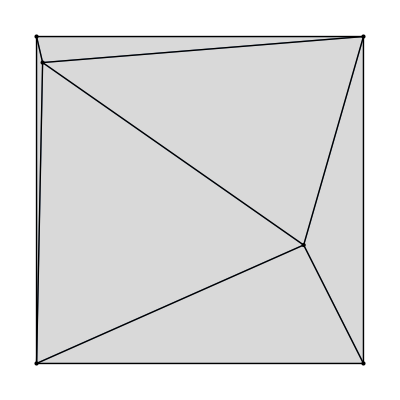

```mathematica
m=RandomOrigami[2]
```

Cells might also render differently.

-Graphics-

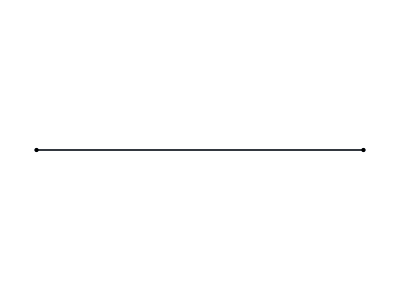

```mathematica
Linkage[{{0,0},{1,0}},{RigidBar[{1,2}],PinnedJoint[2]}]
Origami[{{0,0},{1,0}},{RigidBar[{1,2}],PinnedJoint[2]}]
```

### Extracting information from mechanisms

#### MechanismCellList[]

```mathematica
?MechanismCellList
```

Get a list of all the cells in a mechanism and the data that has been specified.

```mathematica
MechanismCellList[ f=RandomOrigami[1]]
```

{FreeJoint[{1,2,3,4,5}]→{{Shape→Automatic,Label→None,Style→{}},{Shape→Automatic,Label→None,Style→{}},{Shape→Automatic,Label→None,Style→{}},{Shape→Automatic,Label→None,Style→{}},{Shape→Automatic,Label→None,Style→{}}},Face[{{3,5,2},{4,5,3},{5,1,2},{5,4,1}}]→{{FaceStiffness→0,Shape→Automatic,Label→None,Style→{}},{FaceStiffness→0,Shape→Automatic,Label→None,Style→{}},{FaceStiffness→0,Shape→Automatic,Label→None,Style→{}},{FaceStiffness→0,Shape→Automatic,Label→None,Style→{}}},RigidBar[{{1,2},{1,5},{2,3},{2,5},{3,4},{4,1},{5,3},{5,4}}]→{{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}}}}

Get the data for only a specific set of cells of a certain type.

```mathematica
MechanismCellList[ f=RandomOrigami[1], {Face, {{1,5,4},{5,3,4}}}]
```

{Face[{{5,4,1},{4,5,3}}]→{{FaceStiffness→0,Shape→Automatic,Label→None,Style→{}},{FaceStiffness→0,Shape→Automatic,Label→None,Style→{}}}}

```mathematica
MechanismCellList[ f=RandomOrigami[1],Face[{__,1,__}]]
```

{Face[{{2,5,1},{5,4,1}}]→{{FaceStiffness→0,Shape→Automatic,Label→None,Style→{}},{FaceStiffness→0,Shape→Automatic,Label→None,Style→{}}}}

Get data for any cell having data “stiffness” set to Infinity

```mathematica
MechanismCellList[ f=RandomOrigami[1],_,"Stiffness" -> Infinity]
```

{RigidBar[{{1,2},{1,5},{2,3},{2,5},{3,4},{4,1},{5,3},{5,4}}]→{{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}}}}

#### MechanismVertices[], MechanismEdges[], InteriorEdges[], MechanismFaces[]

```mathematica
m=RandomOrigami[3];
```

```mathematica
MechanismVertices[m]
MechanismFaces[m]
MechanismEdges[m]
```

{1,2,3,4,5,6,7}

{{2,5,6},{2,6,1},{3,5,2},{5,7,6},{6,7,1},{7,3,4},{7,4,1},{7,5,3}}

{{2,5},{5,6},{6,2},{6,1},{1,2},{3,5},{2,3},{5,7},{7,6},{7,1},{7,3},{3,4},{4,7},{4,1}}

```mathematica
InteriorEdges[m]
```

{{2,5},{5,6},{6,2},{6,1},{3,5},{5,7},{7,6},{7,1},{7,3},{4,7}}

#### MechanismConnectivity[]

```mathematica
?MechanismConnectivity
```

```mathematica
MechanismConnectivity["Methods"]
```

{{vertices,edges,faces}→{vertices,edges,faces,ordered faces,ordered edges}}

This function is used to work out what vertices, edges, and faces are connected to each other. It returns a list for each element of the left hand side of the rule and indicates all of the objects it is connected to on the right-hand side of the rule. To find all edges connected to each vertex, for example:

```mathematica
MechanismConnectivity[ m=RandomOrigami[3] , "vertices" -> "edges" ]
```

{{{1,7},{1,2},{1,6},{1,4}},{{2,3},{2,5},{2,7},{2,1}},{{3,5},{3,6},{3,4},{3,2}},{{4,6},{4,1},{4,3}},{{5,2},{5,7},{5,3},{5,6}},{{6,5},{6,1},{6,3},{6,4},{6,7}},{{7,2},{7,6},{7,5},{7,1}}}

If the object is oriented (see orientedQ[]) you can get the edges and faces in counterclockwise order.

```mathematica
MechanismConnectivity[ m , "vertices" -> "ordered edges" ]
```

{{{1,2},{1,7},{1,6}},{{2,3},{2,5},{2,7}},{{3,4},{3,6},{3,5}},{{4,1},{4,6}},{{5,7},{5,2},{5,3},{5,6}},{{6,1},{6,7},{6,5},{6,3},{6,4}},{{7,1},{7,2},{7,5},{7,6}}}

### manipulating mechanisms

#### ChangeCellData[]

```mathematica
?ChangeCellData
```

Make some random origami and extract the equilibrium lengths of all the edges.

```mathematica
MechanismCellList[ f= RandomOrigami[3], _RigidBar]
```

{RigidBar[{{1,2},{1,6},{2,3},{2,6},{3,4},{3,5},{4,1},{4,7},{5,4},{5,7},{6,3},{6,5},{7,1},{7,6}}]→{{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}}}}

Change all the length’s of rigidBar’s matching a particular pattern. Notice the order of the indices does not matter.

```mathematica
MechanismCellList[ 
ChangeCellData[ f,RigidBar[{1,_}],"EquilibriumLength"->1 ],
 _RigidBar]
```

{RigidBar[{{1,2},{1,6},{2,3},{2,6},{3,4},{3,5},{4,1},{4,7},{5,4},{5,7},{6,3},{6,5},{7,1},{7,6}}]→{{Stiffness→∞,EquilibriumLength→1,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→1,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→1,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→1,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}}}}

Add labels to a mechanism.

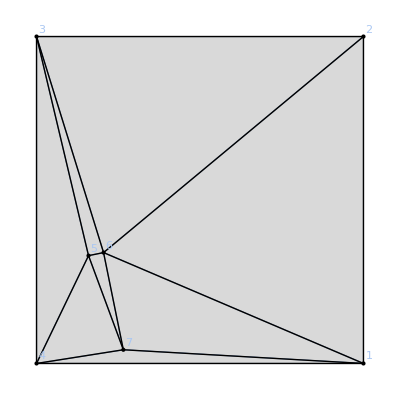

```mathematica
ChangeCellData[f,_FreeJoint,"Label"->"Index" ]
```

#### DeleteCells[]

```mathematica
?DeleteCells
```

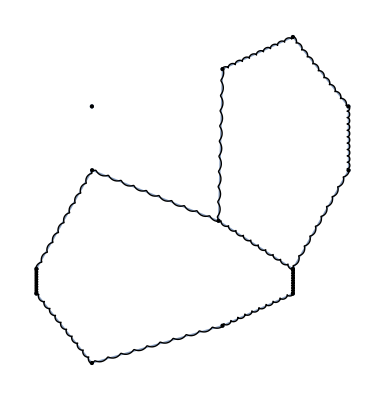

```mathematica
DeleteCells[ RandomCellNetwork[3], _[{1,_}]]
```

delete faces associated with vertex 1.

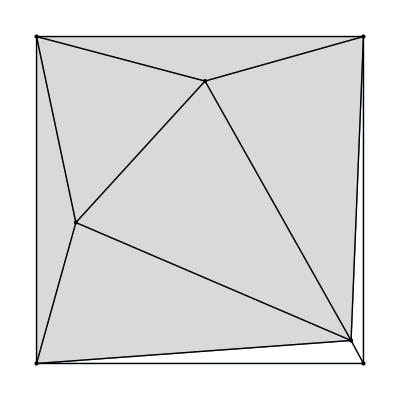

```mathematica
DeleteCells[ f=RandomOrigami[3],Face[{___,1,___}]]
```

Delete all cells associated with vertex 1. Note that the vertex itself remains.

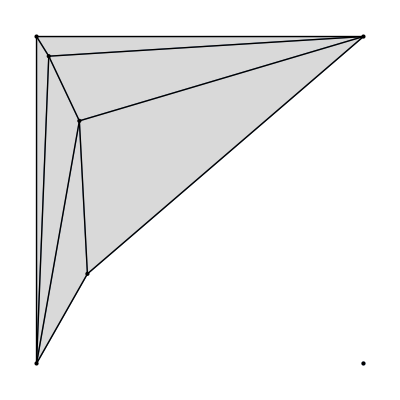

```mathematica
DeleteCells[ f=RandomOrigami[3],_[{___,1,___}]]
```

#### AddCells[]

```mathematica
?AddCells
```

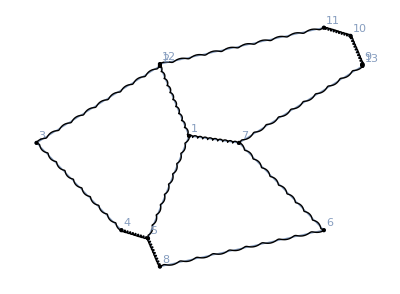

```mathematica
m=ChangeCellData[RandomCellNetwork[3],_FreeJoint,"Label"->"Index"]
```

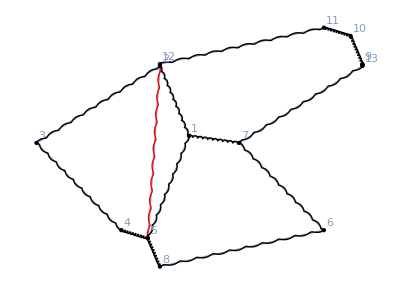

```mathematica
AddCells[ m, { Property[ Spring[{2,5}] , { "Style" -> Red } ]} ]
```

You can also overwrite existing parts of an mechanisms.

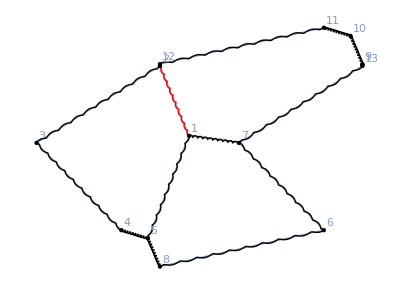

```mathematica
m2=AddCells[ m, { Property[ Spring[{2,1}] , { "Style" -> Red } ]} ]
```

```mathematica
MechanismCellList[m2,Spring[{2,1}]]
```

{Spring[{{2,1}}]→{{Stiffness→∞,EquilibriumLength→Automatic,Strain→((#1-#2)/#2&),Shape→Automatic,Label→None,Style→{RGBColor[1, 0, 0]}}}}

#### deleting and adding vertices with AddCells[] and DeleteVertices[]

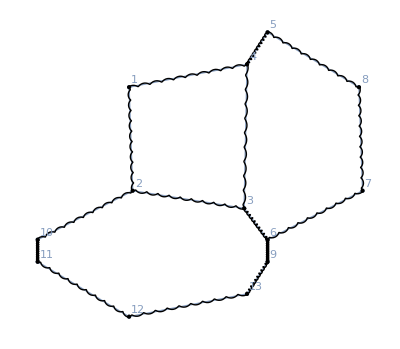

```mathematica
m=ChangeCellData[RandomCellNetwork[3],_FreeJoint,"Label"->"Index"]
```

You can add a vertex with addCell using the notation joint[ name -> position ] where label is a name to use to refer to the point and position are the coordinates of the new vertex. You then refer to the new vertex using its name.

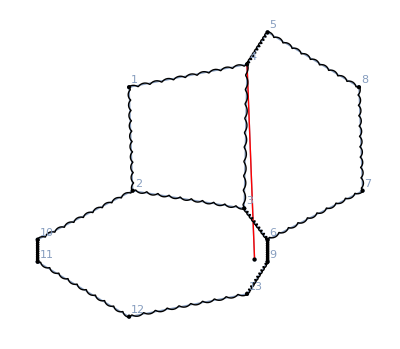

```mathematica
AddCells[ m, {FreeJoint[ "a"->{0,-1/4}], RigidBar[{"a",4},"Style"->Red]}]
```

deleteVertices[] deletes a vertex and everything connected to it.

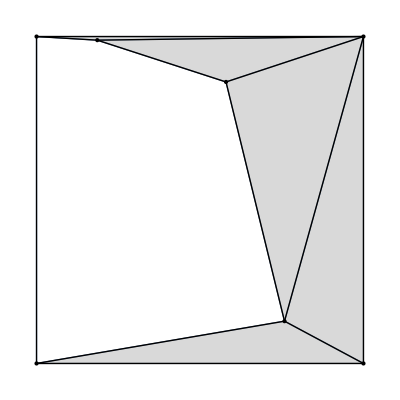

```mathematica
DeleteVertices[ m=RandomOrigami[4], {5}]
```

#### SelectCells[]

```mathematica
?SelectCells
```

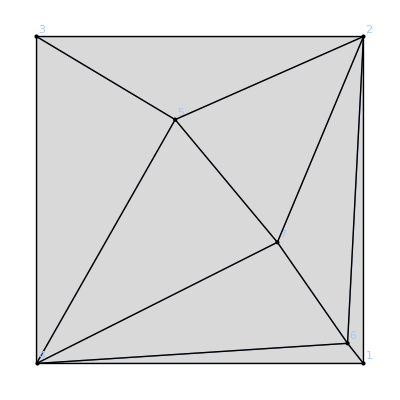

```mathematica
f=ChangeCellData[_FreeJoint,"Label"->"Index"]@RandomOrigami[3]
```

Select all the cells that are joined to vertex 1.

MeshRegion::pnset: Some or all of the properties specified in the Properties option could not be set.

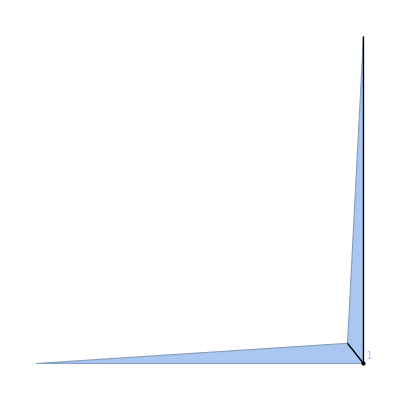

```mathematica
f2=ChangeCellData[_FreeJoint,"Label"->"Index"]@SelectCells[f,_[1]|_[{___,1,___}]]
```

```mathematica
MechanismCellList[f]
```

{FreeJoint[{1,2,3,4,5,6,7}]→{{Shape→Automatic,Label→Index,Style→{}},{Shape→Automatic,Label→Index,Style→{}},{Shape→Automatic,Label→Index,Style→{}},{Shape→Automatic,Label→Index,Style→{}},{Shape→Automatic,Label→Index,Style→{}},{Shape→Automatic,Label→Index,Style→{}},{Shape→Automatic,Label→Index,Style→{}}},Face[{{1,6,4},{2,6,1},{2,7,6},{4,5,3},{4,6,7},{4,7,5},{5,2,3},{5,7,2}}]→{{FaceStiffness→0,Shape→Automatic,Label→None,Style→{}},{FaceStiffness→0,Shape→Automatic,Label→None,Style→{}},{FaceStiffness→0,Shape→Automatic,Label→None,Style→{}},{FaceStiffness→0,Shape→Automatic,Label→None,Style→{}},{FaceStiffness→0,Shape→Automatic,Label→None,Style→{}},{FaceStiffness→0,Shape→Automatic,Label→None,Style→{}},{FaceStiffness→0,Shape→Automatic,Label→None,Style→{}},{FaceStiffness→0,Shape→Automatic,Label→None,Style→{}}},RigidBar[{{1,2},{2,3},{2,5},{3,4},{4,1},{4,5},{4,6},{4,7},{5,3},{5,7},{6,1},{6,2},{7,2},{7,6}}]→{{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}}}}

```mathematica
MechanismCellList[f2]
```

{FreeJoint[{1}]→{{Shape→Automatic,Label→Index,Style→{}}},Face[{{1,6,4},{2,6,1}}]→{{FaceStiffness→0,Shape→Automatic,Label→None,Style→{}},{FaceStiffness→0,Shape→Automatic,Label→None,Style→{}}},RigidBar[{{1,2},{4,1},{6,1}}]→{{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}},{Stiffness→∞,EquilibriumLength→Automatic,Shape→Automatic,Label→None,Style→{}}}}

Keep all the rigid bars connected to vertex 1 but all the faces in the structure.

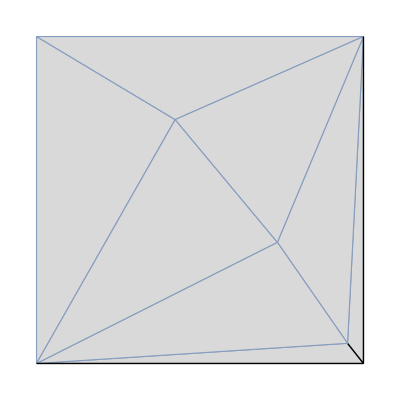

```mathematica
f2=SelectCells[f,Face[_]| RigidBar[{___,1,___}]]
```

#### DisplaceVertices[]

```mathematica
?DisplaceVertices
```

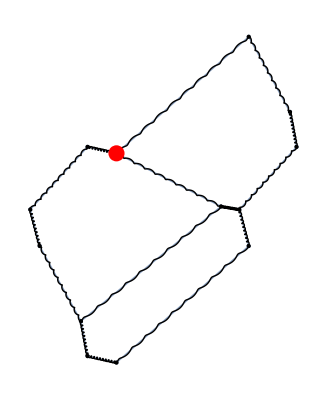
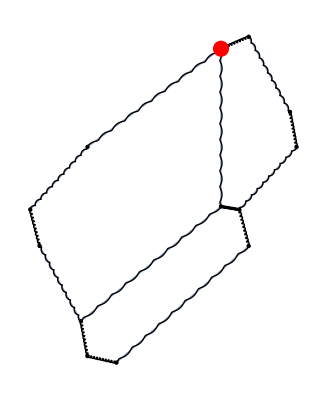

```mathematica
{
f=ChangeCellData[FreeJoint[1],"Style"->{Red,PointSize[0.029]}]@RandomCellNetwork[3],
DisplaceVertices[ f, {1->{0.5,0.5}} ]
}
```

```mathematica
DisplaceVertices[ RandomOrigami[2], RandomReal[ {-0.1,0.1}, {6,3}]]
```

-Graphics3D-

#### SubdivideCell[]

```mathematica
?SubdivideCells
```

Create a vertex on an edge and displace it.

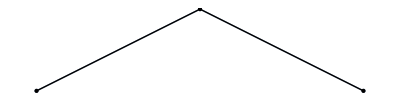

```mathematica
DisplaceVertices[{"a"->{0,1/4}}]@SubdivideCells[Linkage[ {{0,0},{1,0}}, {RigidBar[{1,2}]}],{{1,2}},"a"]
```

#### Henneberg[]

Henneberg operations acting on a 2D linkage preserve the number of degrees of freedom (generically).

```mathematica
?Henneberg
```

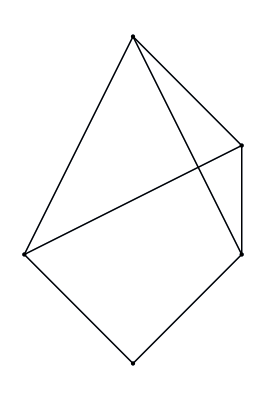

```mathematica
f2=Henneberg[2][ {1,2,"b"}, "a"->{1,1/2} ] @ Henneberg[1][ {1,2}, "c"->{1/2,-1/2} ] @ AddCells[  { FreeJoint[ "b" -> {1/2,1}], RigidBar[{1,"b"}], RigidBar[{2,"b"}]} ] @ Linkage[{{0,0},{1,0}},{RigidBar[{1,2}]}]
```

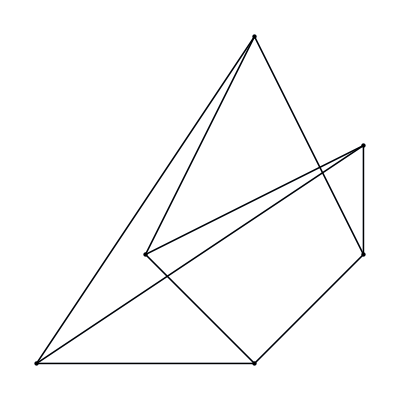

```mathematica
Henneberg[2][{-1/2,-1/2}] @ f2
```

#### JoinMechanism[]

```mathematica
?JoinMechanism
```

```mathematica
JoinMechanism[ RandomOrigami[2], #+{0,0,1}& /@ RandomOrigami[3] ]
```

-Graphics3D-

Two vertices that are sufficiently close together will be merged. Use “overlapPrecision” to specify how close to operate this.

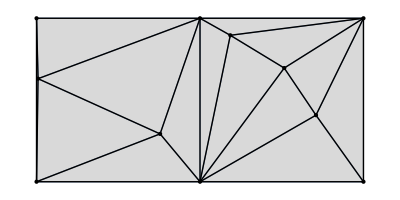

```mathematica
JoinMechanism[ RandomOrigami[2], #+{Sqrt[2],0,0}& /@ RandomOrigami[3] ]
```

## Examples

## basic examples

### building new frameworks

```mathematica
f=Linkage[{{0,0},{1,0}},{RigidBar[{1,2}]}]
```

-Graphics-

There are two formats:

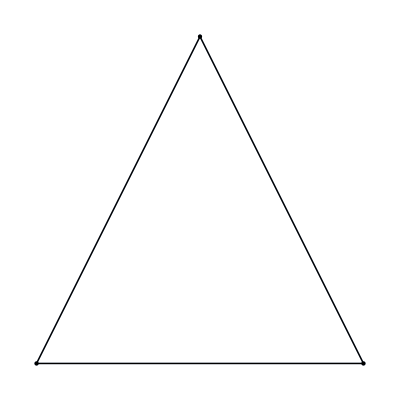

```mathematica
AddCells[ f,  { FreeJoint[ "b" -> {1/2,1}], RigidBar[{1,"b"}], RigidBar[{2,"b"}]} ]
```

```mathematica
AddCells[  { FreeJoint[ "b" -> {1/2,1}], RigidBar[{1,"b"}], RigidBar[{2,"b"}]} ] @ f
```

-Graphics-

This version allows constructions by sequential composition

#### Henneberg operations

```mathematica
?Henneberg
```

```mathematica
f2=Henneberg[2][ {1,2,"b"}, "a"->{1,1/2} ] @ Henneberg[1][ {1,2}, "c"->{1/2,-1/2} ] @ AddCells[  { FreeJoint[ "b" -> {1/2,1}], RigidBar[{1,"b"}], RigidBar[{2,"b"}]} ] @ f
```

-Graphics-

```mathematica
Henneberg[2][{-1/2,-1/2}] @ f2
```

-Graphics-

### special mechanism examples

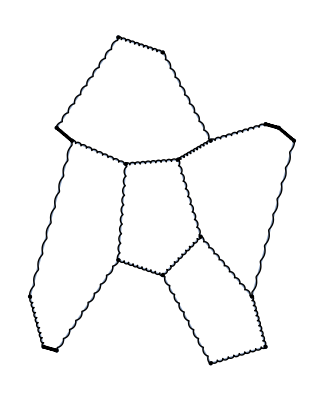

```mathematica
RandomCellNetwork[5]
```

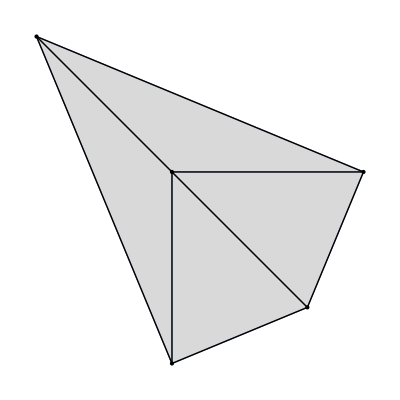

```mathematica
m=SingleVertex[{Pi/4,3Pi/4,3Pi/4,Pi/4}]
```

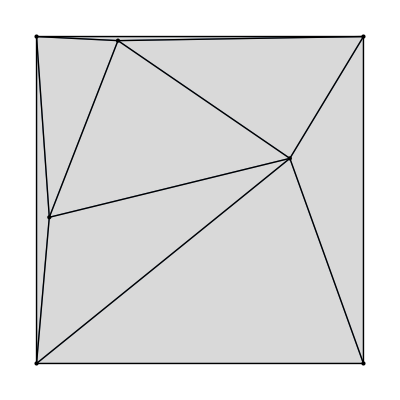

```mathematica
RandomOrigami[3]
```

```mathematica
Linkage["Examples"]
```

{PinnedFourBarLinkage,PolygonalLinkage,ChainLinkage,WattLinkage,ConnellyServatiusLinkage,Connelly2ndOrderRigidLinkage}

```mathematica
?PinnedFourBarLinkage
```

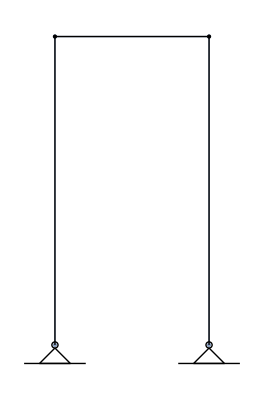

```mathematica
Linkage[PinnedFourBarLinkage[{1/2,1}]]
```

```mathematica
Origami["Examples"]
```

{RandlettBirdOrigami,WaterBombBase,MiuraOriCell}

```mathematica
?WaterBombBase
```

## mechanism examples

### Watt mechanism

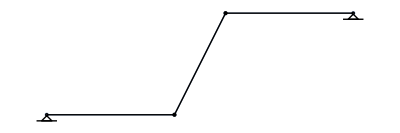

```mathematica
wattMechanism = Linkage[ {{0,0},{1+1/4,0},{2-1/4,1},{3,1}}, {RigidBar[{{1,2},{2,3},{3,4}}], PinnedJoint[1],PinnedJoint[4]} ]
```

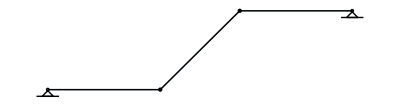

```mathematica
wattMechanism=Linkage[WattLinkage]
```

```mathematica
im=MechanismInfinitesimalMotions[ wattMechanism ,OutputVariables -> v ]
```

{{{0,0},{0,v[1]/(√2)},{0,v[1]/(√2)},{0,0}},{}}

```mathematica
direction = D[im[[1]],v[1]]
```

{{0,0},{0,1/(√2)},{0,1/(√2)},{0,0}}

```mathematica
MechanismZeroModes[wattMechanism]
```

{{{0,0},{0,1},{0,1},{0,0}}}

```mathematica
trajectory = MechanismIsometricTrajectory[ wattMechanism, direction, 100 ];
```

```mathematica
(*The center of the middle bar position *)
centerTrace = Mean /@ trajectory[[All, {2,3}]] ;
centerTrail = Table[ centerTrace[[1;;i]], {i,1,Length[centerTrace]}];
```

```mathematica
ListAnimate @ 
MapThread[
Show[#1,Graphics[{Blue,Point[#2]}]]&,
{
PlotMechanism[ wattMechanism, trajectory ],
centerTrail
}
]
```

### origami bird’s foot vertex

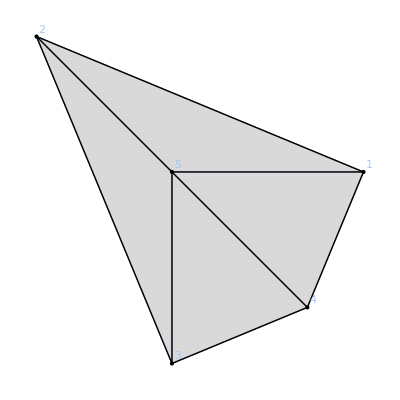

```mathematica
ChangeCellData[_FreeJoint , "Label"->"Index"]@(o=AddCells[ { Property[ TorsionalFold[{1,5}] ,  "Angle"-> Pi/2 ] } ] @SingleVertex[{Pi/4,3Pi/4,3Pi/4,Pi/4}])
```

```mathematica
{en, pos } = MinimizeMechanismEnergy[o]
```

{1.31796×10^-20,{{0.933586,-0.100663,-0.255571},{-0.610404,0.579642,0.497751},{0.118282,-0.916883,-0.304523},{0.606038,-0.617808,0.203841},{-0.0475022,0.0557107,-0.141497}}}

```mathematica
PlotMechanism[o,pos]
```

-Graphics3D-

```mathematica
{ linear, quadratic} = FullSimplify[
MechanismInfinitesimalMotions[o = SingleVertex[{Pi/4,3Pi/4,3Pi/4,Pi/4}], Constraints->{VertexDisplacement[5,All[3]], VertexDisplacement[2,"z"], VertexDisplacement[3,{"x","z"}]} ,
OutputVariables -> v]
]
```

{{{0,0,v[2]},{0,0,0},{0,0,0},{0,0,v[1]},{0,0,0}},{-(v[1] (v[1]-√2 v[2]))/(2 √3)}}

```mathematica
dir = D[ linear /. Solve[quadratic==0,{v[1],v[2]}] /. {v[1]->v,v[2]->v},v]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{{0,0,1},{0,0,0},{0,0,0},{0,0,0},{0,0,0}},{{0,0,1/(√2)},{0,0,0},{0,0,0},{0,0,1},{0,0,0}}}

```mathematica
trajectory1 = Join[
Reverse @MechanismIsometricTrajectory[ o, -dir[[1]],180,Constraints -> {VertexDisplacement[5,All[3]], VertexDisplacement[2,"z"], VertexDisplacement[3,{"x","z"}]},StepSize -> 0.02][[All,{4,1},3]]

,
 MechanismIsometricTrajectory[ o, dir[[1]],180,Constraints ->  {VertexDisplacement[5,All[3]], VertexDisplacement[2,"z"], VertexDisplacement[3,{"x","z"}]}, StepSize-> 0.02][[All,{4,1},3]]
];

trajectory2 = Join[
Reverse @MechanismIsometricTrajectory[ o, -dir[[2]],180,Constraints ->  {VertexDisplacement[5,All[3]], VertexDisplacement[2,"z"], VertexDisplacement[3,{"x","z"}]}, StepSize -> 0.02][[All,{4,1},3]]

,
 MechanismIsometricTrajectory[ o, dir[[2]],180,Constraints -> {VertexDisplacement[5,All[3]], VertexDisplacement[2,"z"], VertexDisplacement[3,{"x","z"}]}, StepSize -> 0.02][[All,{4,1},3]]
];
```

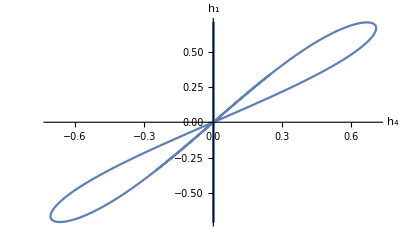

```mathematica
Show[
ListPlot[trajectory1,Joined->True],
ListPlot[trajectory2, Joined->True],

PlotRange->All,AxesLabel->{Subscript["h",4],Subscript["h",1]}
]
```

### pendulum

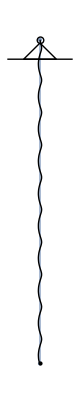

```mathematica
m=Linkage[{{0,0},{0,-1}},{Spring[{1,2},"Stiffness"->30],PinnedJoint[1]}]
```

```mathematica
trajectory=MechanismDynamicalSystem[m,{{{0,0},{Cos[Pi/3],-Sin[Pi/3]}},{{0,0},{0,0}}}, {t,0,20},AddedEnergy->(0.1 VertexPosition[2,"y"]),VertexMass->0.1,VertexDrag->0.001,StartingStepSize->0.0001];
```

```mathematica
ListAnimate[PlotMechanism[m,(trajectory/.t->#)&/@Range[0,20,0.1]]]
```

```mathematica
trajectory2=MechanismDynamicalSystem[ChangeCellData[_Spring,"Stiffness"->1]@m,{{{0,0},{1.3 Cos[Pi/3],-1.3 Sin[Pi/3]}},{{0,0},{0,0}}}, {t,0,20},AddedEnergy->(0.1 VertexPosition[2,"y"]),VertexMass->0.1,VertexDrag->0.1,StartingStepSize->0.0001];
ListAnimate[PlotMechanism[m,(trajectory2/.t->#)&/@Range[0,20,0.1]]]
```

### Connelly’s example of a 2nd order rigid mechanism that is not prestress stable

The following example comes from Example 5.3.1 in Connelly, SIAM J. Discrete Math., 9, 453-491 (1996)

This 3D framework is second-order rigid but not prestress stable. Vertex 2 is on top of 7 and vertex 4 is on top of 8. To avoid identifying these two pairs of vertices with each other, we will add a small displacement to vertices 7 and 8. We define pos below for the correct vertex positions.

```mathematica
m=Linkage[{
{0,0,0},{0,1,0},{0,0,1},
{1,0,0},{1,1,0},{0,1+0.01,0},{1+0.01,0,0}
},{
RigidBar[{
{1,2},{1,3},{1,4},{1,6},{1,7},{2,3},{2,5},{2,7},{3,4},{3,5},{4,5},{4,6},{5,6},{5,7},{6,7}
},"Shape"->RigidBarShape["Width"->0.003]],
PinnedJoint[1],
Property[PinnedJoint[2],"ConstraintFunction"->(#[[{1,3}]]&) ],Property[PinnedJoint[3],"ConstraintFunction"->(#[[1]]&)]
}
]
pos={{0,0,0},{0,1,0},{0,0,1},{1,0,0},{1,1,0},{0,1,0},{1,0,0}};
```

-Graphics3D-

There are two self stresses and two zero modes

```mathematica
ss=MechanismSelfStresses[m,pos]
zm=MechanismZeroModes[m,pos]
```

{{1,0,0,-1,0,0,1,-1,0,0,0,0,-1,0,1,0,0,0,0,0,0},{1,0,-1,-1,1,0,1,-1,0,0,-1,1,-1,1,0,0,0,0,0,0,0}}

{{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,1}},{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,1},{0,0,0}}}

The linear zero modes and quadratic constraints associated with them.

```mathematica
eq=MechanismInfinitesimalMotions[m,pos,OutputVariables->v]
```

{{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,v[2]},{0,0,v[1]}},{√(2/3) v[1] v[2]+v[2]^2/(√6),-√(6/35) v[1]^2-√(10/21) v[1] v[2]+v[2]^2/(√210)}}

The system is second order rigid.

```mathematica
Solve[eq[[2]]==0,{v[1],v[2]}]
```

{{v[1]→0,v[2]→0},{v[1]→0,v[2]→0}}

There is no linear combination of the two quadratic forms that is positive definite. This is equivalent to the mechanism not being prestress stable.

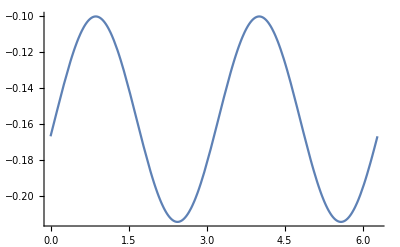

```mathematica
mat=Normal@CoefficientArrays[#,{v[1],v[2]},Symmetric->True][[3]]&/@DeleteCases[eq[[2]],0];
Plot[Det[Cos[t] mat[[1]]+Sin[t] mat[[2]]],{t,0,2Pi}]
```

### Connelly and Servatius’ example of a cusp mechanism

Connelly, R. and Servatius, H., 1994. Higher-order rigidity—What is the proper definition?. Discrete & Computational Geometry, 11(2), pp.193-200.

This is an example of a mechanism that is 3rd order rigid but still has a nontrivial flex. It is constructed from two Watt linkages with equal length bars (which are highlighted below in two different colors).

```mathematica
mA=ChangeCellData[RigidBar,{{1,2},{2,3},{3,4},{4,5}},"Style"->Red]@Linkage[{{-3,0},{-2,0},{-2+1/Sqrt[2]/2,0+1/Sqrt[2]/2},{-2+1/Sqrt[2],0+1/Sqrt[2]},{-1+1/Sqrt[2],1/Sqrt[2]},{-2,1/Sqrt[2]}},{
PinnedJoint[{1,5}],RigidBar[{{1,2},{2,3},{3,4},{4,5},{4,6},{3,6},{2,6}}],
FreeJoint["a"->{-2+1/Sqrt[2]/2,0+1/Sqrt[2]/2}]
}
];
mB=ChangeCellData[RigidBar,{{1,2},{2,3},{3,4},{4,5}},"Style"->Blue]@Linkage[{{3,0},{2,0},{2-1/Sqrt[2]/2,0+1/Sqrt[2]/2},{2-1/Sqrt[2],0+1/Sqrt[2]},{1-1/Sqrt[2],1/Sqrt[2]},{2,1/Sqrt[2]}},{
PinnedJoint[{1,5}],RigidBar[{{1,2},{2,3},{3,4},{4,5},{4,6},{3,6},{2,6}}],
FreeJoint["b"->{2-1/Sqrt[2]/2,0+1/Sqrt[2]/2}]
}
];
```

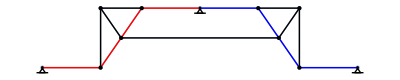

```mathematica
m=AddCells[JoinMechanism[(#+{1-1/Sqrt[2],0})& /@ mA,(#+{-1+1/Sqrt[2],0})& /@ mB],RigidBar[{"a","b"}]]
```

This is a brief animation of the motion.

```mathematica
ListAnimate[PlotMechanism[m,MechanismIsometricTrajectory[m,ReplacePart[ConstantArray[{0,0},m["VertexNumber"]],4->{0,-1}],50]]]
```

```mathematica
ListAnimate[PlotMechanism[m,MechanismIsometricTrajectory[m,ReplacePart[ConstantArray[{0,0},m["VertexNumber"]],10->{0,-1}],50]]]
```

At second order, the mechanism has a degenerate second order flex.

```mathematica
{lin,quad}=FullSimplify@MechanismInfinitesimalMotions[m,OutputVariables->v]
```

{{{0,0},{0,v[2]/2},{0,v[2]/2},{0,v[2]/2},{0,0},{0,v[2]/2},{0,0},{0,v[1]/2},{0,v[1]/2},{0,v[1]/2},{0,v[1]/2}},{-(v[1]-v[2])^2/(2 √(238+104 √2))}}

```mathematica
Solve[quad==0,v[1]]
```

{{v[1]→v[2]},{v[1]→v[2]}}

```mathematica
Eigensystem[D[D[quad[[1]],{{v[1],v[2]}}],{{v[1],v[2]}}]]
```

{{-√(2/(119+52 √2)),0},{{-1,1},{1,1}}}

## periodic mechanisms

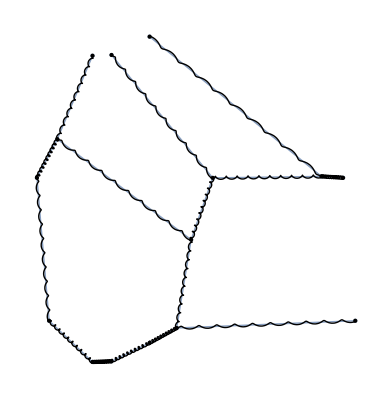

```mathematica
m=MechanismUnitCell[ m0=RandomCellNetwork[5], {{1,0},{0,1}}]
```

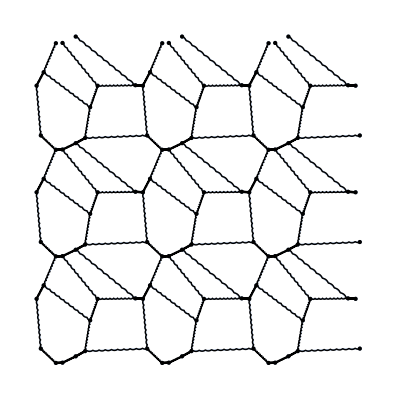

```mathematica
TesselateMechanism[ m , {{1,0},{0,1}},{3,3}]
```

```mathematica
pi=PeriodicIdentification[ m,  {{1,0},{0,1}} ]
```

PeriodicIdentificationData[{{1,0},{0,1}}]

```mathematica
Options[MechanismConstraintMatrix]
```

{Constraints→None,CellPattern→_,ReducedMap→False}

```mathematica
MechanismConstraintMatrix[m, Constraints -> pi["Constraints"], "ReducedMap"->True ]
```

SparseArray[…]

```mathematica
m2=ChangeCellData[m, _Spring ,  "EquilibriumLength" -> 0.05]
```

-Graphics-

```mathematica
{en, pos} = MinimizeMechanismEnergy[m2, Constraints -> pi["Constraints"],MaxIterations->10^4]
```

{305.966,{{-0.060548,0.195322},{-0.233542,0.108421},{-0.1338,-0.0494264},{0.0385281,-0.0255994},{-0.483351,0.171848},{-0.46722,-0.0923714},{-0.20114,-0.228794},{0.279253,-0.214819},{-0.00070126,-0.515963},{0.270797,-0.523822},{-0.720747,-0.214819},{-0.729203,-0.523822},{-0.483351,-0.828152},{-0.233542,-0.891579},{-0.060548,-0.804678}}}

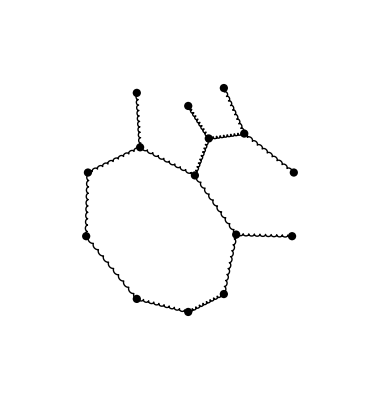

```mathematica
PlotMechanism[ m, pos ]
```